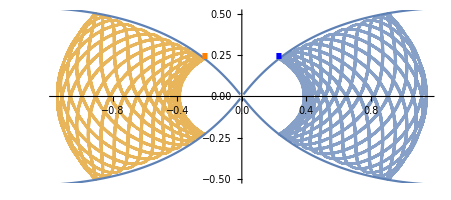

```mathematica
(*Do[{*)tmax=500;θ0=(45*π)/180;r0=(1/(2Cos[θ0])-2/(√(9 Sin[θ0]^2+Cos[θ0]^2)))/(-1/(√3));x0=r0Cos[θ0];y0=r0Sin[θ0];sol=NDSolve[{x''[t]==1/(4 x[t]^2)-x[t]/((x[t]^2+9 y[t]^2)^(3/2)),y''[t]==-(3y[t])/((x[t]^2+9 y[t]^2)^(3/2)),x'[0]==0,y'[0]==0,x[0]==x0,y[0]==y0},{x[t],y[t]},{t,-0.001,tmax}];px=x[t]/.Flatten[sol]⟦1⟧;py=y[t]/.Flatten[sol]⟦2⟧;
(*Data1=Table[px,{t,0,tmax,0.1}];Export["C:\\Users\\19685\\Desktop\\Outx.txt",Data1,"Table"];
Data2=Table[py,{t,0,tmax,0.1}];Export["C:\\Users\\19685\\Desktop\\Outy.txt",Data2,"Table"];*)
(*Export[{ToString[n]<>".png"},Show[ParametricPlot[{{px,py},{-px,py}},{t,-0.001,tmax},PlotStyle->{{Opacity[0.2]},{Opacity[0.2]}},ImageSize->1000],ContourPlot[1/(2Abs[x])-2/(√(x^2+9 y^2))==-1/(√3),{x,-3,3},{y,-1,1},PlotPoints->100],Graphics[{Text[Style["·",FontSize->50,Blue],{x0,y0}],Text[Style["·",FontSize->50,Orange],{-x0,y0}]}]],ImageResolution->100]},{n,3,50,1}]*)
Show[ParametricPlot[{{px,py},{-px,py}},{t,-0.001,tmax},PlotStyle->{{Opacity[0.75]},{Opacity[0.75]}}],ContourPlot[1/(2Abs[x])-2/(√(x^2+9 y^2))==-1/(√3),{x,-3,3},{y,-1,1},PlotPoints->100],Graphics[{Text[Style["·",FontSize->50,Blue],{x0,y0}],Text[Style["·",FontSize->50,Orange],{-x0,y0}]}]]
```